Note to reviewer:
I# corresponds to commutator’s amplitude in the exact light-cone.			IC# to its variation, either inside or outside the light-cone.
1 corresponds to the infrared approximation with X dividing.
2 corresponds to the infrared approximation with T dividing (here Fresnel functions ).
3 corresponds to equation (16) and (17) for I3 and IC3 respectively.
4 corresponds to the infrared approximation with “|k| ≤ m√(M/m-1)√(M/m+1)”, for ω=k/m, the limits turns into |ω|≤√((M/m)^2-1)

In 3 we just considered T=X+δX, with δX>0 outside and δX<0 inside
A ‘C’ before each expression will corresponds to the complex conjugated, that is, Delta2.

```mathematica
IntegrateChangeVariables[Inactive[Integrate][Exp[-I m X Exp[-θ]](1+I m δX Sinh[θ])/Cosh[θ]^(s-1),{θ,-∞,∞}],t,t==Exp[-θ]]
```

ConditionalExpression[(2^(-1+s) ⅇ^(-ⅈ m t X) (1/t+t)^(1-s) (-1+m δX Sin[2 π C[1]+ⅈ Log[t]]))/t, C[1]∈ℤ]t0∞

```mathematica
Simplify[X(a+b)-(X+δX) (a-b)]
```

-a δX+b (2 X+δX)

```mathematica
Factor[-a δX+b (2 X+δX)]
```

2 b X-a δX+b δX

```mathematica
Factor[-b δX+a (2 X+δX)]
```

2 a X+a δX-b δX

```mathematica
TrigReduce[(X+δX) Cosh[θ]+X Sinh[θ]]
```

X Cosh[θ]+δX Cosh[θ]+X Sinh[θ]

```mathematica
FullSimplify[Cosh[x]+Sinh[x]]
```

ⅇ^x

```mathematica
IntegrateChangeVariables[Inactive[Integrate][Exp[-I m X Exp[θ]](1+I m δX Sinh[θ])/Cosh[θ]^(s-1),{θ,-∞,∞}],t,t==Exp[θ]]
```

(2^(-1+s) ⅇ^(-ⅈ m t X) (1/t+t)^(1-s) (1+(ⅈ m (-1+t^2) δX)/(2 t)))/tt0∞

```mathematica
ComplexExpand[Im[ⅇ^(-ⅈ m t X) (1-(ⅈ m (-1+t^2) δX)/(2 t))]]
```

(m δX Cos[m t X])/(2 t)-1/2 m t δX Cos[m t X]-Sin[m t X]

```mathematica
Activate[(2^(-1+s) (1/t+t)^(1-s) ((m δX Cos[m t X])/(2 t)-1/2 m t δX Cos[m t X]-Sin[m t X]))/tt0∞,Unevaluated[Integrate]]
```

ConditionalExpression[-2^(-2+s) (-(2^(1-s) m √π δX Gamma[-1+s/2] HypergeometricPFQ[{-1+s/2},{1/2,1-s/2},(m^2 X^2)/4])/Gamma[1/2 (-1+s)]+(m π (-1+s) s (m^2 X^2)^(1/2 (-2+s)) δX Csc[(π s)/2] HypergeometricPFQ[{-1+s},{-1/2+s/2,s/2},(m^2 X^2)/4])/(2 Gamma[1+s])+(m π (m^2 X^2)^(s/2) δX Csc[(π s)/2] HypergeometricPFQ[{-1+s},{1/2+s/2,1+s/2},(m^2 X^2)/4])/(2 Gamma[1+s])+(m π s X (m^2 X^2)^(1/2 (-2+s)) Csc[(π s)/2] HypergeometricPFQ[{-1+s},{1/2+s/2,s/2},(m^2 X^2)/4])/Gamma[1+s]+(2^(1-s) m √π Gamma[-1+s/2] (δX HypergeometricPFQ[{s/2},{1/2,2-s/2},(m^2 X^2)/4]+2 X HypergeometricPFQ[{s/2},{3/2,2-s/2},(m^2 X^2)/4]))/Gamma[1/2 (-1+s)]), m X∈ℝ&&Re[s]>2]

```mathematica
IC3[m_,X_,δX_,s_]:=-2^(-2+s) (-(2^(1-s) m √π δX Gamma[-1+s/2] HypergeometricPFQ[{-1+s/2},{1/2,1-s/2},(m^2 X^2)/4])/Gamma[1/2 (-1+s)]+(m π (-1+s) s (m^2 X^2)^(1/2 (-2+s)) δX Csc[(π s)/2] HypergeometricPFQ[{-1+s},{-1/2+s/2,s/2},(m^2 X^2)/4])/(2 Gamma[1+s])+(m π (m^2 X^2)^(s/2) δX Csc[(π s)/2] HypergeometricPFQ[{-1+s},{1/2+s/2,1+s/2},(m^2 X^2)/4])/(2 Gamma[1+s])+(m π s X (m^2 X^2)^(1/2 (-2+s)) Csc[(π s)/2] HypergeometricPFQ[{-1+s},{1/2+s/2,s/2},(m^2 X^2)/4])/Gamma[1+s]+(2^(1-s) m √π Gamma[-1+s/2] (δX HypergeometricPFQ[{s/2},{1/2,2-s/2},(m^2 X^2)/4]+2 X HypergeometricPFQ[{s/2},{3/2,2-s/2},(m^2 X^2)/4]))/Gamma[1/2 (-1+s)])
```

```mathematica
CIC3[m_,X_,δX_,s_]:=-IC3[m,X,δX,s]
```

```mathematica
I3[m_,X_,s_]:=IC3[m,X,0,s]
```

```mathematica
CI3[m_,X_,s_]:=-I3[m,X,s]
```

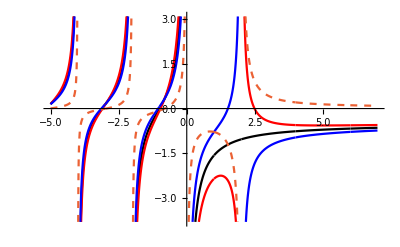

```mathematica
Plot[{IC3[1,2,0,s],IC3[1,2,0.5,s],IC3[1,2,-0.5,s],IC3[1,2,0.5,s]-I3[1,2,s]},{s,-5,7},PlotStyle->{Black,Red,Blue,Dashed}]
```

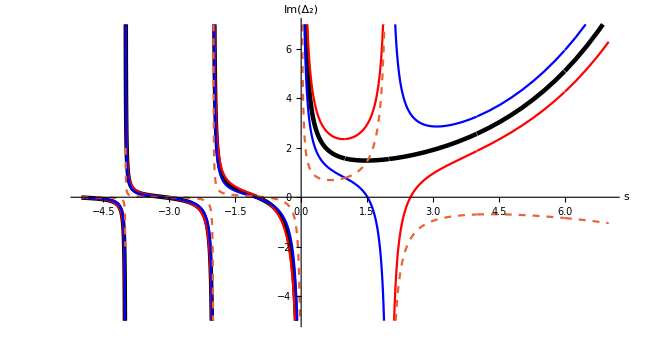

```mathematica
Show[Plot[{1.5^(s-1)*CIC3[1,2,0,s],1.5^(s-1)*CIC3[1,2,0.5,s],1.5^(s-1)*CIC3[1,2,-0.5,s],1.5^(s-1)*(CIC3[1,2,0.5,s]-CI3[1,2,s])},{s,-5,7},PlotRange->{-5,7}, PlotStyle->{{Black,Thickness[0.005]},Red,Blue,Dashed},AxesLabel->{s,Im[Subscript[Δ, 2]]}],ImageSize->{645,357},AspectRatio->Full]
```

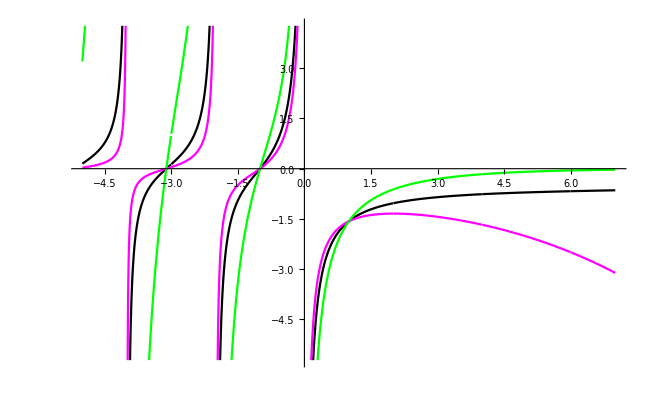

```mathematica
Plot[{I3[1,2,s],1.3^(s-1) *I3[1,2,s],0.6^(s-1) *I3[1,2,s]},{s,-5,7},PlotStyle->{Black,Magenta,Green}]
```

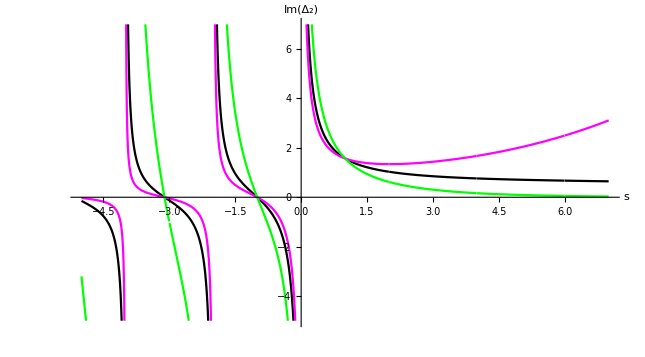

```mathematica
Show[Plot[{CI3[1,2,s],1.3^(s-1) *CI3[1,2,s],0.6^(s-1) *CI3[1,2,s]},{s,-5,7},PlotRange->{-5,7}, PlotStyle->{Black,Magenta,Green},AxesLabel->{s,Im[Subscript[Δ, 2]]}],ImageSize->{645,357},AspectRatio->Full]
```

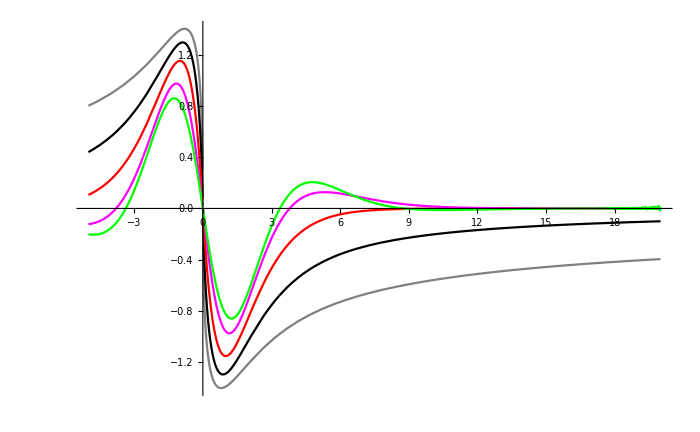

```mathematica
Plot[{I3[1,X,1.5],-(2 Sinh[X]-2 EulerGamma Sinh[X]-Log[X^2] Sinh[X]-X Derivative[{0},{0,1},0][HypergeometricPFQ][{1},{1,3/2},X^2/4]-X Derivative[{0},{0,1},0][HypergeometricPFQ][{1},{3/2,1},X^2/4]-X Derivative[{0},{1,0},0][HypergeometricPFQ][{1},{1,3/2},X^2/4]-2 X Derivative[{1},{0,0},0][HypergeometricPFQ][{1},{1,3/2},X^2/4]+X Derivative[{1},{0,0},0][HypergeometricPFQ][{1},{3/2,1},X^2/4]),I3[1,X,3],I3[1,X,5],I3[1,X,7]},{X,-5,20},PlotStyle->{Gray,Black,Red,Magenta,Green}]
```

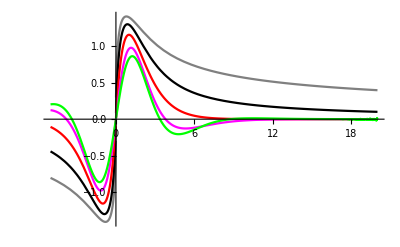

```mathematica
Plot[{CI3[1,X,1.5],2 Sinh[X]-2 EulerGamma Sinh[X]-Log[X^2] Sinh[X]-X Derivative[{0},{0,1},0][HypergeometricPFQ][{1},{1,3/2},X^2/4]-X Derivative[{0},{0,1},0][HypergeometricPFQ][{1},{3/2,1},X^2/4]-X Derivative[{0},{1,0},0][HypergeometricPFQ][{1},{1,3/2},X^2/4]-2 X Derivative[{1},{0,0},0][HypergeometricPFQ][{1},{1,3/2},X^2/4]+X Derivative[{1},{0,0},0][HypergeometricPFQ][{1},{3/2,1},X^2/4],CI3[1,X,3],CI3[1,X,5],CI3[1,X,7]},{X,-5,20},PlotStyle->{Gray,Black,Red,Magenta,Green}]
```

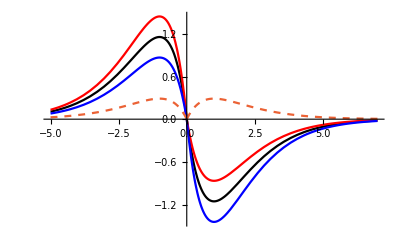

```mathematica
Plot[{IC3[1,X,0,3],IC3[1,X,0.25,3],IC3[1,X,-0.25,3],IC3[1,X,0.25,3]-I3[1,X,3]},{X,-5,7},PlotStyle->{Black,Red,Blue,Dashed}]
```

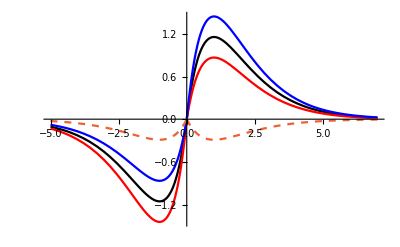

```mathematica
Plot[{CIC3[1,X,0,3],CIC3[1,X,0.25,3],CIC3[1,X,-0.25,3],CIC3[1,X,0.25,3]-CI3[1,X,3]},{X,-5,7},PlotStyle->{Black,Red,Blue,Dashed}]
```

```mathematica
Normal[Simplify[Series[Exp[-I Sqrt[m^2+k^2]T],{k,0,2}],Assumptions->m>0]]
```

ⅇ^(-ⅈ m T)-(ⅈ ⅇ^(-ⅈ m T) k^2 T)/(2 m)

```mathematica
ExpToTrig[ⅇ^(-ⅈ m T)-(ⅈ ⅇ^(-ⅈ m T) k^2 T)/(2 m)]
```

Cos[m T]-(ⅈ k^2 T Cos[m T])/(2 m)-ⅈ Sin[m T]-(k^2 T Sin[m T])/(2 m)

```mathematica
Integrate[(Cos[m T]-(w^2 T Sin[m T])/2)(1-s w^2/2)Cos[m X w],{w,-1,1}]
```

(-2 m^2 X^2 Cos[m T] (2 m s X Cos[m X]+(-2 s+m^2 (-2+s) X^2) Sin[m X])+T Sin[m T] (4 m X (-6 s+m^2 (-1+s) X^2) Cos[m X]+(24 s+4 m^2 (1-3 s) X^2+m^4 (-2+s) X^4) Sin[m X]))/(2 m^5 X^5)

```mathematica
R1[m_,X_,T_,s_]:=(-2 m^2 X^2 Cos[m T] (2 m s X Cos[m X]+(-2 s+m^2 (-2+s) X^2) Sin[m X])+T Sin[m T] (4 m X (-6 s+m^2 (-1+s) X^2) Cos[m X]+(24 s+4 m^2 (1-3 s) X^2+m^4 (-2+s) X^4) Sin[m X]))/(2 m^5 X^5)
```

```mathematica
-Integrate[((w^2 m T Cos[m T])/2+ Sin[m T])(1-s w^2/2)Cos[m X w],{w,-1,1}]
```

(4 m X^2 Sin[m T] (2 m s X Cos[m X]+(-2 s-2 m^2 X^2+m^2 s X^2) Sin[m X])+2 T Cos[m T] (4 m X (-m^2 X^2+s (-6+m^2 X^2)) Cos[m X]+(4 m^2 X^2-2 m^4 X^4+s (24-12 m^2 X^2+m^4 X^4)) Sin[m X]))/(4 m^4 X^5)

```mathematica
FullSimplify[(4 m X^2 Sin[m T] (2 m s X Cos[m X]+(-2 s-2 m^2 X^2+m^2 s X^2) Sin[m X])+2 T Cos[m T] (4 m X (-m^2 X^2+s (-6+m^2 X^2)) Cos[m X]+(4 m^2 X^2-2 m^4 X^4+s (24-12 m^2 X^2+m^4 X^4)) Sin[m X]))/(4 m^4 X^5)]
```

(2 m X^2 Sin[m T] (2 m s X Cos[m X]+(-2 s+m^2 (-2+s) X^2) Sin[m X])+T Cos[m T] (4 m X (-6 s+m^2 (-1+s) X^2) Cos[m X]+(24 s+4 m^2 (1-3 s) X^2+m^4 (-2+s) X^4) Sin[m X]))/(2 m^4 X^5)

```mathematica
I1[m_,X_,T_,s_]:=(2 m X^2 Sin[m T] (2 m s X Cos[m X]+(-2 s+m^2 (-2+s) X^2) Sin[m X])+T Cos[m T] (4 m X (-6 s+m^2 (-1+s) X^2) Cos[m X]+(24 s+4 m^2 (1-3 s) X^2+m^4 (-2+s) X^4) Sin[m X]))/(2 m^4 X^5)
```

```mathematica
CI1[m_,X_,T_,s_]:=-I1[m,X,T,s]
```

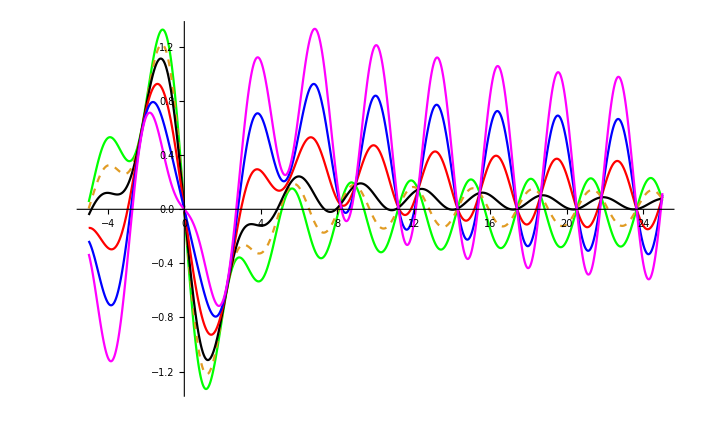

```mathematica
Plot[{I1[1,X,X,1],I1[1,X,X,1.5],I1[1,X,X,2],I1[1,X,X,3],I1[1,X,X,4],I1[1,X,X,5]},{X,-5,25},PlotStyle->{Green,Dashed,Black, Red, Blue, Magenta}]
```

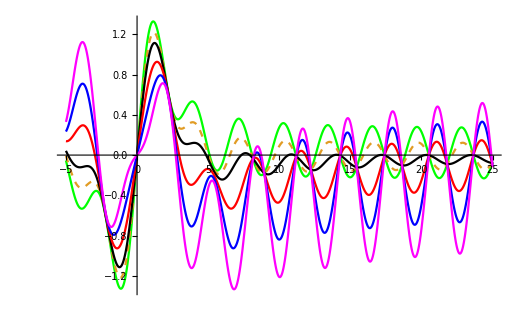

```mathematica
Plot[{CI1[1,X,X,1],CI1[1,X,X,1.5],CI1[1,X,X,2],CI1[1,X,X,3],CI1[1,X,X,4],CI1[1,X,X,5]},{X,-5,25},PlotStyle->{Green,Dashed,Black, Red, Blue, Magenta}]
```

```mathematica
Normal[Series[R1[m,X+δX,X,2],{δX,0,1}]]
```

-(2 δX (-6 m^3 X^2 Cos[m X]^2-60 m X Cos[m X] Sin[m X]+6 m^2 X Cos[m X] Sin[m X]+7 m^3 X^3 Cos[m X] Sin[m X]-2 m^4 X^3 Cos[m X] Sin[m X]+60 Sin[m X]^2-27 m^2 X^2 Sin[m X]^2+m^4 X^4 Sin[m X]^2))/(m^5 X^5)+(-8 m^2 X^2 Cos[m X] (m X Cos[m X]-Sin[m X])+X Sin[m X] (4 m X (-12+m^2 X^2) Cos[m X]+(48-20 m^2 X^2) Sin[m X]))/(2 m^5 X^5)

```mathematica
RC1[m_,X_,δX_,s_]:=-(2 δX (-6 m^3 X^2 Cos[m X]^2-60 m X Cos[m X] Sin[m X]+6 m^2 X Cos[m X] Sin[m X]+7 m^3 X^3 Cos[m X] Sin[m X]-2 m^4 X^3 Cos[m X] Sin[m X]+60 Sin[m X]^2-27 m^2 X^2 Sin[m X]^2+m^4 X^4 Sin[m X]^2))/(m^5 X^5)+(-8 m^2 X^2 Cos[m X] (m X Cos[m X]-Sin[m X])+X Sin[m X] (4 m X (-12+m^2 X^2) Cos[m X]+(48-20 m^2 X^2) Sin[m X]))/(2 m^5 X^5)
```

```mathematica
Normal[Series[I1[m,X+δX,X,2],{δX,0,1}]]
```

(2 (-12 m X Cos[m X]^2+m^3 X^3 Cos[m X]^2+12 Cos[m X] Sin[m X]-3 m^2 X^2 Cos[m X] Sin[m X]-2 m X Sin[m X]^2))/(m^4 X^4)-(2 δX (-60 m X Cos[m X]^2+7 m^3 X^3 Cos[m X]^2+60 Cos[m X] Sin[m X]-21 m^2 X^2 Cos[m X] Sin[m X]+m^4 X^4 Cos[m X] Sin[m X]-6 m X Sin[m X]^2+2 m^3 X^3 Sin[m X]^2))/(m^4 X^5)

```mathematica
IC1[m_,X_,δX_,s_]:=(2 (-12 m X Cos[m X]^2+m^3 X^3 Cos[m X]^2+12 Cos[m X] Sin[m X]-3 m^2 X^2 Cos[m X] Sin[m X]-2 m X Sin[m X]^2))/(m^4 X^4)-(2 δX (-60 m X Cos[m X]^2+7 m^3 X^3 Cos[m X]^2+60 Cos[m X] Sin[m X]-21 m^2 X^2 Cos[m X] Sin[m X]+m^4 X^4 Cos[m X] Sin[m X]-6 m X Sin[m X]^2+2 m^3 X^3 Sin[m X]^2))/(m^4 X^5)
```

```mathematica
CIC1[m_,X_,δX_,s_]:=-IC1[m,X,δX,s]
```

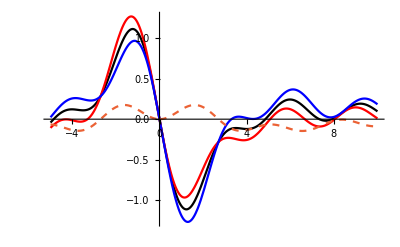

```mathematica
Plot[{IC1[1,X,0,2],IC1[1,X,0.5,2],IC1[1,X,-0.5,2],IC1[1,X,0.5,2]-I1[1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full]
```

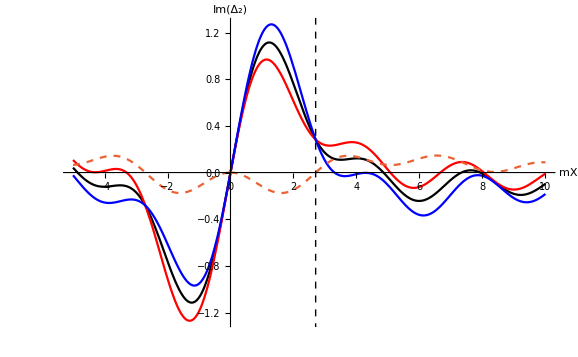

```mathematica
Plot[{CIC1[1,X,0,2],CIC1[1,X,0.5,2],CIC1[1,X,-0.5,2],CIC1[1,X,0.5,2]-CI1[1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full,AxesStyle->Gray,Ticks->None,Epilog->{Dashed,Line[{{2.703741563164931,-100},{2.703741563164931,100}}]},AxesLabel->{mX,Im[Subscript[Δ, 2]]}]
```

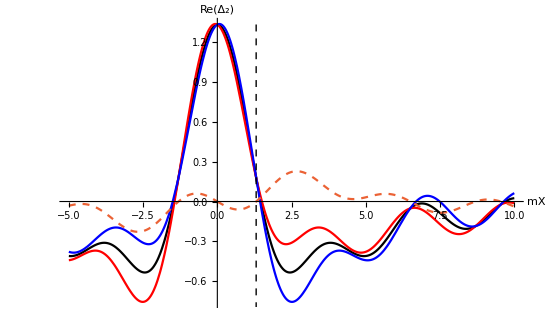

```mathematica
Plot[{RC1[1,X,0,2],RC1[1,X,0.5,2],RC1[1,X,-0.5,2],RC1[1,X,0.5,2]-R1[1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full,AxesStyle->Gray,Ticks->None,Epilog->{Dashed,Line[{{1.307489090190902,-100},{1.307489090190902,100}}]},AxesLabel->{mX,Re[Subscript[Δ, 2]]}]
```

```mathematica
FindRoot[RC1[1,X,0.5,2]-R1[1,X,X,2],{X,2}]
```

{X→1.30749}

```mathematica
Series[Sqrt[1+w^2],{w,0,2}]
```

1+w^2/2+O[w]^3

```mathematica
Integrate[(1-s w^2/2)Exp[-I m T (1+w^2/2)]Cos[m X w],{w,-1,1}]
```

1/(m^(3/2) T^(5/2))(1/8+ⅈ/8) (-2 ⅈ ⅇ^(-ⅈ m T+(ⅈ m X^2)/(2 T)) m √π T^2 (Erf[((1/2+ⅈ/2) √m (T-X))/(√T)]-Erf[((1/2+ⅈ/2) √m (-T+X))/(√T)]+2 Erf[((1/2+ⅈ/2) √m (T+X))/(√T)])+ⅇ^(-1/2 ⅈ m (3 T+2 X)) s ((-2-2 ⅈ) √m √T (T-X+ⅇ^(2 ⅈ m X) (T+X))+ⅇ^((ⅈ m (T+X)^2)/(2 T)) √π (T+ⅈ m X^2) (Erf[((1/2+ⅈ/2) √m (T-X))/(√T)]-Erf[((1/2+ⅈ/2) √m (-T+X))/(√T)]+2 Erf[((1/2+ⅈ/2) √m (T+X))/(√T)])))

```mathematica
Integrate[(1-s w^2/2)Cos[m T (1+w^2/2)]Cos[m X w],{w,-1,1}]
```

1/(4 m^(3/2) T^(5/2))(4 m √π T^2 (Cos[m (T-X^2/(2 T))] (FresnelC[(√m (T-X))/(√π √T)]+FresnelC[(√m (T+X))/(√π √T)])-(FresnelS[(√m (T-X))/(√π √T)]+FresnelS[(√m (T+X))/(√π √T)]) Sin[m (T-X^2/(2 T))])-s (2 √m √T (T+X) Sin[m ((3 T)/2-X)]+2 √m √T (T-X) Sin[m ((3 T)/2+X)]-√π FresnelC[(√m (-T-X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])+√π FresnelC[(√m (T-X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])-√π FresnelC[(√m (-T+X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])+√π FresnelC[(√m (T+X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])+√π FresnelS[(√m (-T-X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])-√π FresnelS[(√m (T-X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])+√π FresnelS[(√m (-T+X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])-√π FresnelS[(√m (T+X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])))

```mathematica
-Integrate[(1-s w^2/2)Sin[m T (1+w^2/2)]Cos[m X w],{w,-1,1}]
```

-1/(4 m^(3/2) T^(5/2))(4 m √π T^2 (Cos[m (T-X^2/(2 T))] (FresnelS[(√m (T-X))/(√π √T)]+FresnelS[(√m (T+X))/(√π √T)])+(FresnelC[(√m (T-X))/(√π √T)]+FresnelC[(√m (T+X))/(√π √T)]) Sin[m (T-X^2/(2 T))])-s (-2 √m √T (T+X) Cos[m ((3 T)/2-X)]+2 √m √T (-T+X) Cos[m ((3 T)/2+X)]-√π FresnelS[(√m (-T-X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])+√π FresnelS[(√m (T-X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])-√π FresnelS[(√m (-T+X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])+√π FresnelS[(√m (T+X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])-√π FresnelC[(√m (-T-X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])+√π FresnelC[(√m (T-X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])-√π FresnelC[(√m (-T+X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])+√π FresnelC[(√m (T+X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])))

```mathematica
I2[m_,X_,T_,s_]:=-1/(4 m^(3/2) T^(5/2))(4 m √π T^2 (Cos[m (T-X^2/(2 T))] (FresnelS[(√m (T-X))/(√π √T)]+FresnelS[(√m (T+X))/(√π √T)])+(FresnelC[(√m (T-X))/(√π √T)]+FresnelC[(√m (T+X))/(√π √T)]) Sin[m (T-X^2/(2 T))])-s (-2 √m √T (T+X) Cos[m ((3 T)/2-X)]+2 √m √T (-T+X) Cos[m ((3 T)/2+X)]-√π FresnelS[(√m (-T-X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])+√π FresnelS[(√m (T-X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])-√π FresnelS[(√m (-T+X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])+√π FresnelS[(√m (T+X))/(√π √T)] (m X^2 Cos[m (T-X^2/(2 T))]-T Sin[m (T-X^2/(2 T))])-√π FresnelC[(√m (-T-X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])+√π FresnelC[(√m (T-X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])-√π FresnelC[(√m (-T+X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])+√π FresnelC[(√m (T+X))/(√π √T)] (T Cos[m (T-X^2/(2 T))]+m X^2 Sin[m (T-X^2/(2 T))])))
```

```mathematica
CI2[m_,X_,T_,s_]:=-I2[m,X,T,s]
```

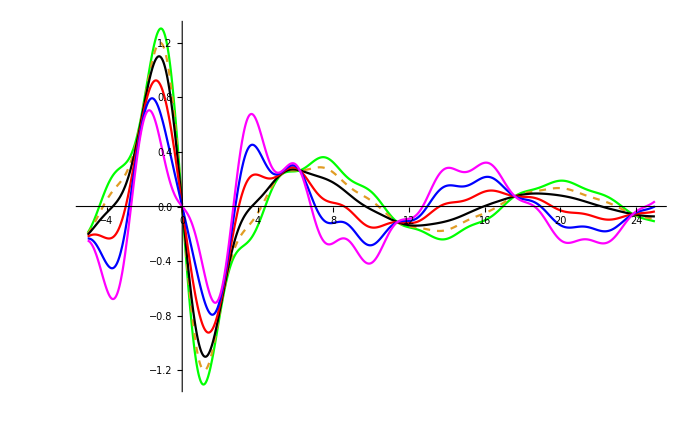

```mathematica
Plot[{I2[1,X,X,1],I2[1,X,X,1.5],I2[1,X,X,2],I2[1,X,X,3],I2[1,X,X,4],I2[1,X,X,5]},{X,-5,25},PlotStyle->{Green,Dashed,Black,Red,Blue,Magenta}]
```

```mathematica
Normal[Series[I2[m,X+δX,X,s],{δX,0,1}]]
```

(-4 m √π X^2 (Cos[(m X)/2] FresnelS[(2 √m √X)/(√π)]+FresnelC[(2 √m √X)/(√π)] Sin[(m X)/2])-s (4 √m X^(3/2) Cos[(m X)/2]-2 √π FresnelS[(2 √m √X)/(√π)] (m X^2 Cos[(m X)/2]-X Sin[(m X)/2])-2 √π FresnelC[(2 √m √X)/(√π)] (X Cos[(m X)/2]+m X^2 Sin[(m X)/2])))/(4 m^(3/2) X^(5/2))+1/(2 m X^2)δX (-2 s Cos[(m X)/2]+s Cos[(m X)/2] Cos[2 m X]+s Cos[(5 m X)/2]+2 m^(3/2) √π X^(3/2) Cos[(m X)/2] FresnelC[(2 √m √X)/(√π)]-m^(3/2) √π s X^(3/2) Cos[(m X)/2] FresnelC[(2 √m √X)/(√π)]+3 √m √π s √X Cos[(m X)/2] FresnelS[(2 √m √X)/(√π)]+2 m X Sin[(m X)/2]-3 m s X Sin[(m X)/2]-2 m X Cos[2 m X] Sin[(m X)/2]+m s X Cos[2 m X] Sin[(m X)/2]+3 √m √π s √X FresnelC[(2 √m √X)/(√π)] Sin[(m X)/2]-2 m^(3/2) √π X^(3/2) FresnelS[(2 √m √X)/(√π)] Sin[(m X)/2]+m^(3/2) √π s X^(3/2) FresnelS[(2 √m √X)/(√π)] Sin[(m X)/2]-2 m X Cos[(m X)/2] Sin[2 m X]+m s X Cos[(m X)/2] Sin[2 m X]-s Sin[(m X)/2] Sin[2 m X])

```mathematica
IC2[m_,X_,δX_,s_]:=(-4 m √π X^2 (Cos[(m X)/2] FresnelS[(2 √m √X)/(√π)]+FresnelC[(2 √m √X)/(√π)] Sin[(m X)/2])-s (4 √m X^(3/2) Cos[(m X)/2]-2 √π FresnelS[(2 √m √X)/(√π)] (m X^2 Cos[(m X)/2]-X Sin[(m X)/2])-2 √π FresnelC[(2 √m √X)/(√π)] (X Cos[(m X)/2]+m X^2 Sin[(m X)/2])))/(4 m^(3/2) X^(5/2))+1/(2 m X^2)δX (-2 s Cos[(m X)/2]+s Cos[(m X)/2] Cos[2 m X]+s Cos[(5 m X)/2]+2 m^(3/2) √π X^(3/2) Cos[(m X)/2] FresnelC[(2 √m √X)/(√π)]-m^(3/2) √π s X^(3/2) Cos[(m X)/2] FresnelC[(2 √m √X)/(√π)]+3 √m √π s √X Cos[(m X)/2] FresnelS[(2 √m √X)/(√π)]+2 m X Sin[(m X)/2]-3 m s X Sin[(m X)/2]-2 m X Cos[2 m X] Sin[(m X)/2]+m s X Cos[2 m X] Sin[(m X)/2]+3 √m √π s √X FresnelC[(2 √m √X)/(√π)] Sin[(m X)/2]-2 m^(3/2) √π X^(3/2) FresnelS[(2 √m √X)/(√π)] Sin[(m X)/2]+m^(3/2) √π s X^(3/2) FresnelS[(2 √m √X)/(√π)] Sin[(m X)/2]-2 m X Cos[(m X)/2] Sin[2 m X]+m s X Cos[(m X)/2] Sin[2 m X]-s Sin[(m X)/2] Sin[2 m X])
```

```mathematica
CIC2[m_,X_,δX_,s_]:=-IC2[m,X,δX,s]
```

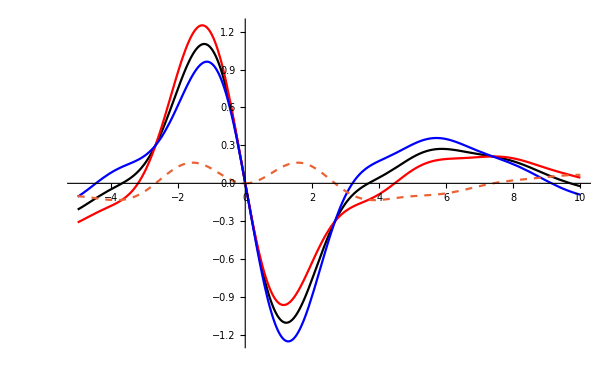

```mathematica
Plot[{IC2[1,X,0,2],IC2[1,X,0.5,2],IC2[1,X,-0.5,2],IC2[1,X,0.5,2]-I2[1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full]
```

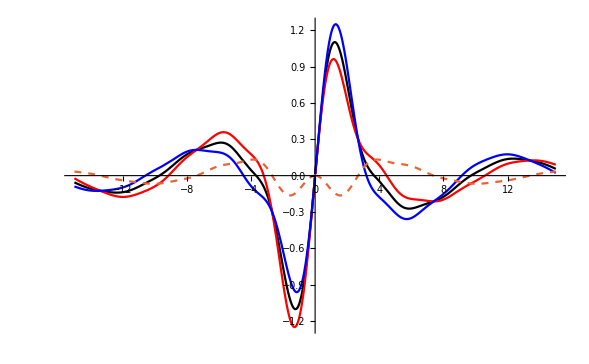

```mathematica
Plot[{CIC2[1,X,0,2],CIC2[1,X,0.5,2],CIC2[1,X,-0.5,2],CIC2[1,X,0.5,2]-CI2[1,X,X,2]},{X,-15,15},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full]
```

```mathematica
Integrate[(1-s w^2/2)(Sin[m T]+w^2 m T Cos[m T]/2)Cos[m X w],{w,-Sqrt[(M/m)^2-1],Sqrt[(M/m)^2-1]}]
```

1/(2 m^4 X^5)(2 m X^2 Sin[m T] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 m^2 X^2+s (2+m^2 X^2-M^2 X^2)) Sin[m √(-1+M^2/m^2) X])+T Cos[m T] (4 m √(-1+M^2/m^2) X (m^2 X^2+s (6+m^2 X^2-M^2 X^2)) Cos[m √(-1+M^2/m^2) X]-(2 m^2 X^2 (2+m^2 X^2-M^2 X^2)+s (24-12 M^2 X^2+m^4 X^4+M^4 X^4-2 m^2 X^2 (-6+M^2 X^2))) Sin[m √(-1+M^2/m^2) X]))

```mathematica
FullSimplify[%1]
```

1/(2 m^4 X^5)(2 m X^2 Sin[m T] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X])+T Cos[m T] (4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X]))

```mathematica
I4[M_,m_,X_,T_,s_]:=1/(8π m^4 X^4)(M/m)^(s-1)(2 m X Sin[m T] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X])+T/X Cos[m T] (4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X]))
```

```mathematica
Normal[Series[I4[M,m,X+δX,X,s],{δX,0,1}]]
```

1/(8 m^4 π X^4)(M/m)^(-1+s) (2 m X Sin[m X] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X])+Cos[m X] (4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X]))+1/(8 m^4 π)(M/m)^(-1+s) δX (-1/X^5 4 (2 m X Sin[m X] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X])+Cos[m X] (4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X]))+1/X^4(2 m Sin[m X] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X]+X (2 m^3 √(-1+M^2/m^2) X^2 Cos[m √(-1+M^2/m^2) X]+m^3 √(-1+M^2/m^2) s X^2 Cos[m √(-1+M^2/m^2) X]-m M^2 √(-1+M^2/m^2) s X^2 Cos[m √(-1+M^2/m^2) X]+4 m^2 X Sin[m √(-1+M^2/m^2) X]))+X Cos[m X] (-(4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X])/X^2+1/X(-m √(-1+M^2/m^2) (24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Cos[m √(-1+M^2/m^2) X]-(8 (-3 M^2 s+m^2 (1+3 s)) X+4 (m-M) (m+M) (-M^2 s+m^2 (2+s)) X^3) Sin[m √(-1+M^2/m^2) X]+4 m √(-1+M^2/m^2) ((6 s+3 (-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Sin[m √(-1+M^2/m^2) X])))))

```mathematica
IC4[M_,m_,X_,δX_,s_]:=1/(8 m^4 π X^4)(M/m)^(-1+s) (2 m X Sin[m X] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X])+Cos[m X] (4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X]))+1/(8 m^4 π)(M/m)^(-1+s) δX (-1/X^5 4 (2 m X Sin[m X] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X])+Cos[m X] (4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X]))+1/X^4(2 m Sin[m X] (-2 m √(-1+M^2/m^2) s X Cos[m √(-1+M^2/m^2) X]+(2 s+(-M^2 s+m^2 (2+s)) X^2) Sin[m √(-1+M^2/m^2) X]+X (2 m^3 √(-1+M^2/m^2) X^2 Cos[m √(-1+M^2/m^2) X]+m^3 √(-1+M^2/m^2) s X^2 Cos[m √(-1+M^2/m^2) X]-m M^2 √(-1+M^2/m^2) s X^2 Cos[m √(-1+M^2/m^2) X]+4 m^2 X Sin[m √(-1+M^2/m^2) X]))+X Cos[m X] (-(4 m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-(24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Sin[m √(-1+M^2/m^2) X])/X^2+1/X(-m √(-1+M^2/m^2) (24 s+4 (-3 M^2 s+m^2 (1+3 s)) X^2+(m-M) (m+M) (-M^2 s+m^2 (2+s)) X^4) Cos[m √(-1+M^2/m^2) X]-(8 (-3 M^2 s+m^2 (1+3 s)) X+4 (m-M) (m+M) (-M^2 s+m^2 (2+s)) X^3) Sin[m √(-1+M^2/m^2) X]+4 m √(-1+M^2/m^2) ((6 s+3 (-M^2 s+m^2 (1+s)) X^2) Cos[m √(-1+M^2/m^2) X]-m √(-1+M^2/m^2) X (6 s+(-M^2 s+m^2 (1+s)) X^2) Sin[m √(-1+M^2/m^2) X])))))
```

```mathematica
AI4[M_]:=Plot[{I4[M,1,X,X,0.5],I4[M,1,X,X,1],I4[M,1,X,X,1.5],I4[M,1,X,X,2],I4[M,1,X,X,3],I4[M,1,X,X,4],I4[M,1,X,X,5]},{X,-5,25},PlotStyle->{Brown,Green,Dashed,Black,Red,Blue,Magenta}]
```

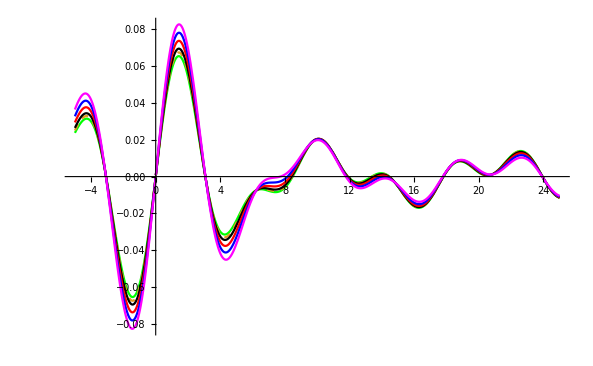

```mathematica
AI4[1.1]
```

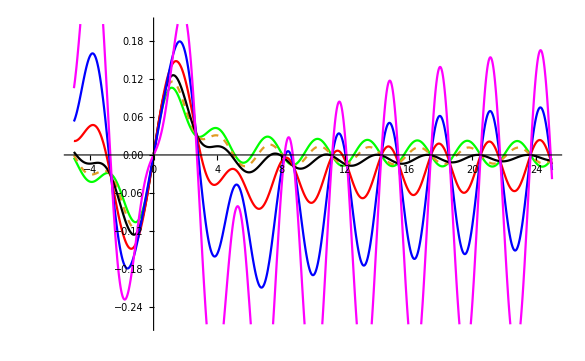

```mathematica
AI4[Sqrt[2]]
```

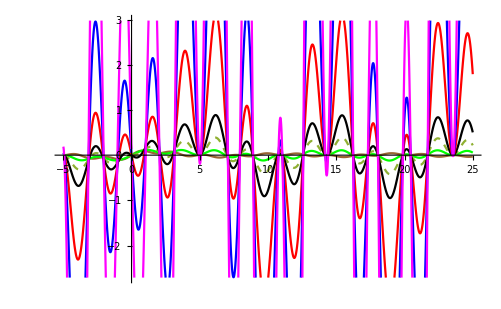

```mathematica
AI4[2]
```

```mathematica
GI4[M_]:=Plot[{IC4[M,1,X,0,2],IC4[M,1,X,0.5,2],IC4[M,1,X,-0.5,2],IC4[M,1,X,0.5,2]-I4[M,1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full]
```

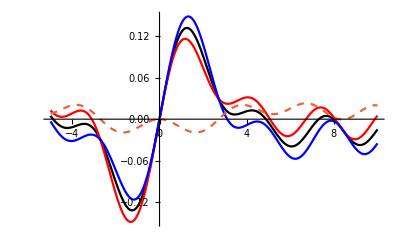

```mathematica
GI4[1.5]
```

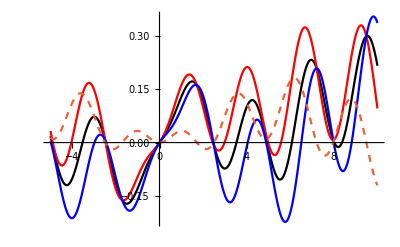

```mathematica
GI4[1.75]
```

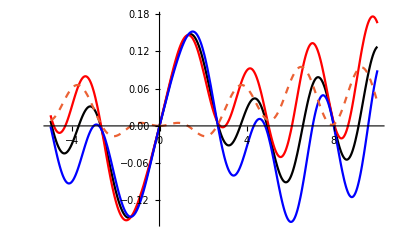

```mathematica
GI4[1.65]
```

```mathematica
FindRoot[IC4[M,1,2,0.5,2]-I4[M,1,2,2,2],{M,1.7}]
```

{M→2.10797}

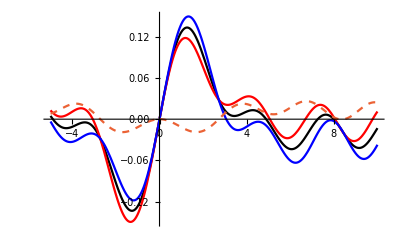

```mathematica
Plot[{IC4[Sqrt[2]+0.1,1,X,0,2],IC4[Sqrt[2]+0.1,1,X,0.5,2],IC4[Sqrt[2]+0.1,1,X,-0.5,2],IC4[Sqrt[2]+0.1,1,X,0.5,2]-I4[Sqrt[2]+0.1,1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full]
```

```mathematica
Plot[{IC4[Sqrt[2],1,X,0,2],IC4[Sqrt[2],1,X,0.5,2],IC4[Sqrt[2],1,X,-0.5,2],IC4[Sqrt[2],1,X,0.5,2]-I4[Sqrt[2],1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full]
```

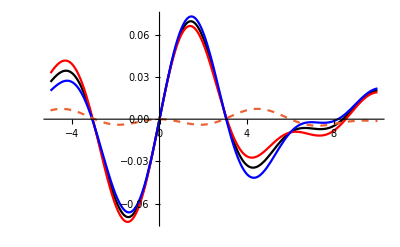

```mathematica
Plot[{IC4[1.1,1,X,0,2],IC4[1.1,1,X,0.5,2],IC4[1.1,1,X,-0.5,2],IC4[1.1,1,X,0.5,2]-I4[1.1,1,X,X,2]},{X,-5,10},PlotStyle->{Black,Red,Blue,Dashed},PlotRange->Full]
```